# Ionization Cross Section

```mathematica
Q[U_]=Log[U]/(U^m El^2)
```

(U^-m Log[U])/El^2

```mathematica
U[E0_]=E0/El
```

E0/El

Compute relative to  E0

```mathematica
Simplify[D[Q[U[E0]],E0]]
```

((E0/El)^(-1-m) (1-m Log[E0/El]))/El^3

```mathematica
Simplify[D[Q[U[E0]],E0]==(1-m Log[U[E0]])/(U[E0]^(1+m)El^3)]
```

True

Reexpress the derivative wrt m

```mathematica
Simplify[D[Q[U],m]==-Q[U]Log[U]]
```

True

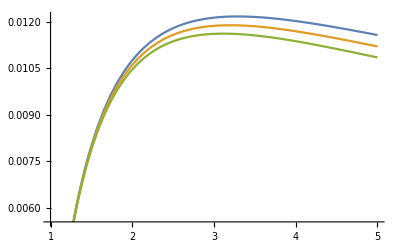

```mathematica
Plot[{Q[U]/.{m->0.84,El-> 6},Q[U]/.{m->0.86,El-> 6},Q[U]/.{m->0.88,El-> 6}},{U,1,5}]
```